```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY189/sec_int_data/778nm.dat"]
```

{{1.63065,-0.0440146},{1.58758,-0.0316661},{1.51023,-0.0393959},{1.46132,-0.0276076},{1.41705,-0.0238215},{1.38078,-0.0296657},{1.34407,-0.00941417},{1.30453,-0.0168105},{1.27782,-0.0203864},{1.24828,-0.0259539},{1.22646,-0.0282349},{1.20042,-0.00781042},{1.183,-0.0122345},{1.16401,-0.00651115},{1.14739,-0.013146},{1.13423,-0.0117083},{1.12389,-0.016658},{1.11401,-0.256946},{1.10574,-0.119989},{1.09905,-0.201504},{1.09389,-0.189032},{1.08918,-0.0729794},{1.08895,-0.0644745},{1.08874,-0.0634191},{1.08738,0.00727348},{1.08767,0.0163654},{1.08994,-0.00355632},{1.0948,-0.00169143},{1.10288,0.00349389},{1.1168,0.0168571},{1.12832,0.000099995},{1.1517,0.00945516},{1.18117,0.0176434},{1.20042,0.00149888},{1.25083,0.00019998},{1.28067,-0.00712532},{1.3108,0.0116321},{1.33715,-0.000870379}}

-0.117285+0.0687898 x

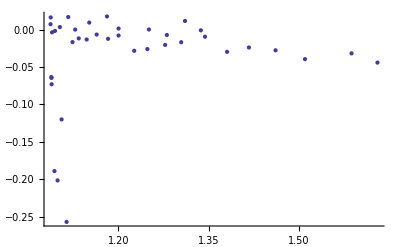

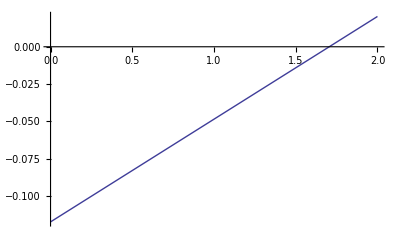

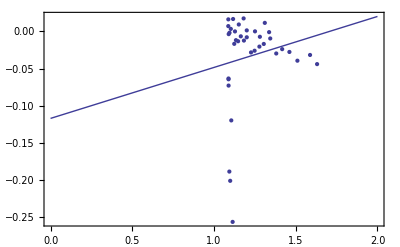

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```